# Casimir fits - symmetric

this is a specialized version for symmetric hadrons

## Definitions

```mathematica
PrepareData[data_]:=Module[{selector,l,new,i},
l=Length[data];selector={1,0,1};
(*pick out E and J*)
new=Pick[data,ConstantArray[selector,l],1] ;
(*change the ordering of J and E*)
new[[All,{1,2}]]=new[[All,{2,1}]];
(*square the energy*)
new[[All,2]]=new[[All,2]]^2 ;
new]
Bisect[xmin_,xmax_,f_,accur_:10^-5]:=Module[{x1=N[xmin],x2=N[xmax],xmid=N[(xmin+xmax)/2],step=0},(*Print[{step,Maxsteps,Abs[f[xmid]]>accur}]*)

 While[Abs[f[xmid]]>accur,
If[Sign[Re[f[x1]f[xmid]]]>0,
x1=xmid,
x2=xmid];
xmid=N[(x1+x2)/2];
Sign[f[x1]f[xmid]]];
xmid]
Δθmax=Evaluate[Δθ /. FindRoot[1-Δθ/(2*Cos[Δθ/2]),{Δθ,1.2}]];
(*sign=+1 is repulsive case*)
(*eom 1*)
Feq[β_,m_,q_,T_,ω_,Δθ_,sign_,a_,Spin_]:=T √(1-β^2)-(m β ω)/(√(1-β^2))+((a-Spin) ω^2)/(4 β^2)-1/(2 (Δθ+β^2 Sin[Δθ])^3)q^2 sign ω^2 (β (β^2 Cos[Δθ]+(2+β^2-2 Δθ^2) Cos[Δθ]+β^2 Cos[2 Δθ]+2 Δθ Sin[Δθ])+β (2+3 β^2+2 β^4+2 β^2 (1+β^2) Cos[Δθ]+2 β^2 Δθ Sin[Δθ]))
(*actually sign=1 in the following *)
Feqsol[β_?NumericQ,m_?NumericQ,q_?NumericQ,T_?NumericQ,Δθ_?NumericQ,sign_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=(2 (-6 m β^7 Δθ-4 m β^3 Δθ^3+6 m β^7 Δθ Cos[2 Δθ]-3 m β^9 Sin[Δθ]-12 m β^5 Δθ^2 Sin[Δθ]+m β^9 Sin[3 Δθ]+2 √(β^2 (Δθ+β^2 Sin[Δθ])^3 (4 m^2 β^4 (Δθ+β^2 Sin[Δθ])^3+T (1-β^2)^(3/2) (16 q^2 sign β^3+24 q^2 sign β^5+16 q^2 sign β^7-6 a β^4 Δθ+6 Spin β^4 Δθ-4 a Δθ^3+4 Spin Δθ^3+16 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (4 q^2 sign β+3 a Δθ-3 Spin Δθ) Cos[2 Δθ]-3 a β^6 Sin[Δθ]+3 Spin β^6 Sin[Δθ]+16 q^2 sign β^3 Δθ Sin[Δθ]+16 q^2 sign β^5 Δθ Sin[Δθ]-12 a β^2 Δθ^2 Sin[Δθ]+12 Spin β^2 Δθ^2 Sin[Δθ]+a β^6 Sin[3 Δθ]-Spin β^6 Sin[3 Δθ])))))/(√(1-β^2) (16 q^2 sign β^3+24 q^2 sign β^5+16 q^2 sign β^7-6 a β^4 Δθ+6 Spin β^4 Δθ-4 a Δθ^3+4 Spin Δθ^3+16 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (4 q^2 sign β+3 a Δθ-3 Spin Δθ) Cos[2 Δθ]-3 a β^6 Sin[Δθ]+3 Spin β^6 Sin[Δθ]+16 q^2 sign β^3 Δθ Sin[Δθ]+16 q^2 sign β^5 Δθ Sin[Δθ]-12 a β^2 Δθ^2 Sin[Δθ]+12 Spin β^2 Δθ^2 Sin[Δθ]+a β^6 Sin[3 Δθ]-Spin β^6 Sin[3 Δθ]))/.{a-> (2a)/π,Spin-> (2Spin)/π};

(*eom 3 (actually a geometrical equation)*)
eqΔθ[β_,Δθ_]:=Δθ^2-2 β^2-2 β^2 Cos[Δθ];
(*so actually in this case Δθ/2 = β Cos[Δθ/2]*)
(*get ω,β2,Δθ*)
ModelDynamics[β_?NumericQ,m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=Module[{ω,Δθ,T=1/(2π α)},
Δθ=Δθ/.FindRoot[eqΔθ[β,Δθ],{Δθ,Δθmax}];
(*If[Δθ>Δθmax,Δθ=Δθmax,Δθ=Δθ];*)
ω=Feqsol[β,m,q,T,Δθ,sign,a,Spin];
{ω,Δθ}];
(*get check goodness of solution for eom*)
CheckSol[β_,m_,q_,α_,sign_,a_,Spin_]:=Module[{β2,Δθ,ω,T=1/(2π α)},
{ω,Δθ}=ModelDynamics[β,m,α,q,sign,a,Spin];
{Feq[β,m,q,T,ω,Δθ,sign,a,Spin],eqΔθ[β,Δθ]}]

energy[β_?NumericQ,m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_,Spin_]:=Module[{γ,L,ω,Δθ,T=1/(2π α)},
If[β==0,

(*-T +sign q^2/L^2-(a-Spin)/L^2==0 *)
L=√(2π α)√(sign q^2-(a-Spin));
2m+T L+(sign q^2)/L-(a-Spin)/L,

{ω,Δθ}=ModelDynamics[β,m,α,q,sign,a,Spin]; 
γ=N[1/Sqrt[1-β^2]];
2γ m+(2T)/ω ArcSin[β]+(sign q^2 ω)/(Δθ+Sin[Δθ] β^2)-ω(a-Spin)/(2β)]]

j[β_?NumericQ,m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=Module[{γ,ω,Δθ,T=1/(2π α)},
If[β==0,0,
γ=1/Sqrt[1-β^2];
{ω,Δθ}=ModelDynamics[β,m,α,q,sign,a,Spin];
γ (2m)/ω β^2 +T/(2 ω^2)(2ArcSin[β]-(2β)/γ )-2(sign q^2 β^2 Cos[Δθ])/(Δθ+Sin[Δθ] β^2)]]

βJ[J_?NumericQ,m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_,Spin_,accur_:10^-5]:=
Module[{β,βmin,βmax,jJ},
βmin=0;βmax=1-10^-15;
jJ=(j[#,m,α,q,sign,a,Spin]-J)&;
β=Bisect[βmin,βmax,jJ,accur]];

EJ[J_?NumericQ,m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=
Module[{β},
β=βJ[J,m,α,q,sign,a,Spin];
energy[β,m,α,q,sign,a,Spin]];

ListTraj[m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_?NumericQ,Spin_?NumericQ,βmin_?NumericQ,βmax_?NumericQ,dβ_?NumericQ]:=Module[{x},
Cases[ParallelTable[If[j[x,m,α,q,sign,a,Spin]<1,Null,{energy[x,m,α,q,sign,a,Spin]^2,j[x,m,α,q,sign,a,Spin]}],{x,βmin,βmax ,dβ}],Except[Null]]];

χ2[data_,m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=Module[{lst,χ},
lst=Table[((EJ[data[[i,1]],m,α,q,sign,a,Spin]^2-data[[i,2]])/data[[i,2]])^2,{i,Length[data]}];
Mean[lst]]

χ2opta[data_,α_?NumericQ,m_?NumericQ,q_?NumericQ,sign_?NumericQ,Spin_?NumericQ]:=Module[{a,amin,amax,Δa,lst,χ},
(*a<Spin*)
amin=-1;amax=Spin-Spin/100;Δa=0.05;
lst=Table[{a,χ2[data,m,α,q,sign,a,Spin]},{a,amin,amax,Δa}];
χ=Interpolation[lst];
a=a/. FindMinimum[{χ[a],amin<a<amax},{a}][[2]];
{χ2[data,m,α,q,sign,a,Spin],a}]

χ2l[data_]:=Module[{e,J,lst},e=LinearModelFit[data,J,J];
lst=Table[((e[data[[i,1]]]-data[[i,2]])/data[[i,2]])^2,{i,Length[data]}];
{Mean[lst],e}]
LogarithmicScaling[x_,min_,max_]:=Log[x/min]/Log[max/min]

grapha[data_,α_?NumericQ,Mmin_?NumericQ,Mmax_?NumericQ,q_?NumericQ,sign_?NumericQ,Spin_?NumericQ]:=
Module[{scale},
scale=χ2opta[data,α,(Mmin+Mmax)/2,q,sign,Spin][[1]];
Plot[{χ2opta[data,α,m,q,sign,Spin][[1]]/scale ,χ2opta[data,α,m,q,sign,Spin][[2]]},{m,Mmin,Mmax},PlotLegends->{χ^2/Subscript[(χ^2), mid],Intercept}]];
savefile[]:=FrontEndExecute[FrontEndToken["Save"]];
```

# Casimir fits - highly non symmetric

use the masses of the light quarks from the symmetric fits. Assume stationary charm quark.

## Definitions

```mathematica
SetUMass[m_]:=uMass=m;
(*sign=+1 is repulsive case*)
(*eom 1*)
FeqCharm[β_,m_,q_,T_,ω_,sign_,a_,Spin_]:=T √(1-β^2)-(uMass β ω)/(√(1-β^2))+((a-Spin) ω^2-q^2 sign ω^2)/β^2
(*get ω,β2*)
ModelDynamicsCharm[β_?NumericQ,m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=Module[{ω,T=1/(2π α)},
ω=ω/.FindRoot[FeqCharm[β,m,q,T,ω,sign,a,Spin],{ω,(T(1-β^2))/(m β)}];
ω];
(*get check goodness of solution for eom*)
(*CheckSol[β_,m_,q_,α_,sign_,a_,Spin_]:=Module[{β2,Δθ,ω,T=1/(2π α)},
{ω,Δθ}=ModelDynamics[β,m,α,q,sign,a,Spin];
{Feq[β,m,q,T,ω,Δθ,sign,a,Spin],eqΔθ[β,Δθ]}]*)

energyCharm[β_?NumericQ,m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_,Spin_]:=Module[{γ,L,ω,Δθ,T=1/(2π α)},
If[β==0,

(*-T +sign q^2/L^2-(a-Spin)/L^2==0 *)
L=√(2π α)√(sign q^2-(a-Spin));
m+uMass+T L+(sign q^2)/L-(a-Spin)/L,

ω=ModelDynamicsCharm[β,m,α,q,sign,a,Spin]; 
γ=N[1/Sqrt[1-β^2]];
γ uMass+m+T/ω ArcSin[β]+(sign q^2 ω)/β-ω(a-Spin)/β]]

jCharm[β_?NumericQ,m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=Module[{γ,ω,Δθ,T=1/(2π α)},
If[β==0,0,
γ=1/Sqrt[1-β^2];
ω=ModelDynamicsCharm[β,m,α,q,sign,a,Spin];
γ uMass/ω β^2+T/(2 ω^2)(ArcSin[β]-β/γ )]]

βJCharm[J_?NumericQ,m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_,Spin_,accur_:10^-5]:=
Module[{β,βmin,βmax,jJ},
βmin=0;βmax=1-10^-15;
jJ=(jCharm[#,m,α,q,sign,a,Spin]-J)&;
β=Bisect[βmin,βmax,jJ,accur]];

EJCharm[J_?NumericQ,m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=
Module[{β},
β=βJCharm[J,m,α,q,sign,a,Spin];
energyCharm[β,m,α,q,sign,a,Spin]];

ListTrajCharm[m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_?NumericQ,Spin_?NumericQ,βmin_?NumericQ,βmax_?NumericQ,dβ_?NumericQ]:=Module[{x},
Cases[ParallelTable[If[jCharm[x,m,α,q,sign,a,Spin]<1,Null,{energyCharm[x,m,α,q,sign,a,Spin]^2,jCharm[x,m,α,q,sign,a,Spin]}],{x,βmin,βmax ,dβ}],Except[Null]]];

χ2Charm[data_,m_?NumericQ,α_?NumericQ,q_?NumericQ,sign_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=Module[{lst,χ},
lst=Table[((EJCharm[data[[i,1]],m,α,q,sign,a,Spin]^2-data[[i,2]])/data[[i,2]])^2,{i,Length[data]}];
Mean[lst]]

χ2optaCharm[data_,α_?NumericQ,m_?NumericQ,q_?NumericQ,sign_?NumericQ,Spin_?NumericQ]:=Module[{a,amin,amax,Δa,lst,χ},
(*a<Spin*)
amin=-1;amax=Spin-Spin/100;Δa=0.05;
lst=Table[{a,χ2Charm[data,m,α,q,sign,a,Spin]},{a,amin,amax,Δa}];
χ=Interpolation[lst];
a=a/. FindMinimum[{χ[a],amin<a<amax},{a}][[2]];
{χ2Charm[data,m,α,q,sign,a,Spin],a}]

graphaCharm[data_,α_?NumericQ,Mmin_?NumericQ,Mmax_?NumericQ,q_?NumericQ,sign_?NumericQ,Spin_?NumericQ]:=
Module[{scale},
scale=χ2optaCharm[data,α,(Mmin+Mmax)/2,q,sign,Spin][[1]];
Plot[{χ2optaCharm[data,α,m,q,sign,Spin][[1]]/scale ,χ2optaCharm[data,α,m,q,sign,Spin][[2]]},{m,Mmin,Mmax},PlotLegends->{χ^2/Subscript[(χ^2), mid],Intercept}]];
```

# Mass differences Functions

```mathematica
M[key_,a_]:= 2 √(1/(2π 10^-6 α[key]))√(1/137 Q[key]-a);

TotM[key_,a_]:=M[key,a]+m1[key]+m2[key];

ImplicitΔm[key1_,key2_,a_]:=Mass[key1]-Mass[key2]-M[key1,a]+M[key2,a];

Δmsq[key1_,key2_,a1_,a2_]:=TotM[key1,a1]^2-TotM[key2,a2]^2;

errBars[num_,key1_,key2_,MassUncertainty_,a1_,a2_]:=Block[{errs},
errs=Sort[{ImplicitΔm[key1,key2,a1],ImplicitΔm[key1,key2,a2]},#1<#2&]+{-MassUncertainty,MassUncertainty};
List[{num,errs[[1]]},{num,errs[[2]]}]]

DTable[pnts_List]:=Append[{DTable[Drop[pnts,-1]]},DTable[Take[pnts,-1]]]/;Length[pnts]>1
DTable[pnts_List]:={DTable@@pnts[[1]]}/;Length[pnts]==1
DTable[pnts_List]:=List[]/;Length[pnts]==0
DTable[uM_,α_,cM_]:=Block[{χ,a,dm},
SetUMass[uM];
{χ,a}=χ2optaCharm[PrepareData[Dz],α 10^-6,cM,√(1/137),1,0]/{χ2l[PrepareData[Dz]][[1]],1};
dm=1869.61- 1864.84-2 √(1/(2π 10^-6 α))√(1/137 2/9-a)+2 √(1/(2π 10^-6 α))√(-1/137 4/9-a);
{uM,α,cM,a,dm,χ}]

DTableMod[pnts_List]:=Append[{DTableMod[Drop[pnts,-1]]},DTableMod[Take[pnts,-1]]]/;Length[pnts]>1
DTableMod[pnts_List]:={DTableMod@@pnts[[1]]}/;Length[pnts]==1
DTableMod[pnts_List]:=List[]/;Length[pnts]==0
DTableMod[uM_,α_,cM_]:=Block[{χ,a,dm},
SetUMass[uM];
{χ,a}=χ2optaCharm[PrepareData[Dz],α 10^-6,cM,√(1/137),1,0]/{χ2l[PrepareData[Dz]][[1]],1};
dm=1869.61- 1864.84-√(1/(2π 10^-6 α))√(1/137 2/9-a)+√(1/(2π 10^-6 α))√(-1/137 4/9-a);
{uM,α,cM,a,dm,χ}]
```

# Fitting to data - L fit

## Data points

## Light unflavored mesons

```mathematica
(*meson={mass,Δm,AM}, masses in MeV*)
πzero={{134.9766,0.0006,0},{1229.5,3.2,1},{1672.2,3,2},{2032,3,3},{2250,3,4}(*last two in further states*)};
π0={{1229.5,3.2,1},{1672.2,3,2},{2032,3,3},{2250,3,4}(*last two in further states*)};
η={(*{547.862,0.018,0}*){1170,20,1},{1617,5,2},{2025,5,3},{2328,5,4}(*last two in further states*)};
η0={{547.862,0.018,0},{1170,20,1},{1617,5,2},{2025,5,3},{2328,5,4}(*last two in further states*)};
ρ770={{775.26,0.25,0},{1318.3,0.5,1},{1688.8,2.1,2},{1996,9,3},{2350,35,4},{2450,35,5}};
(*η958={{957.78,0.06,0},{1170,20,1},{1617,5,2}};*)(*check!*)
ω0={{782.65,0.12,0},{1275.1,1.2,1},{1667,4,2},{2018,11,3}(*,{2469,29,6}*)};
ω={(*{782.65,0.12,0},*){1275.1,1.2,1},{1667,4,2},{2018,11,3}(*,{2469,29,6}*)};
az={{980,20,1},{1465,25,2},{1732,16,3},{1982,14,4}}; (*spin = 1*)
ϕ={{1020,20,0},{1525,20,1},{1854,20,2}(*,{1982,14,4}*)}; (*spin = 1*)
(*and more...*)
```

## Strange

```mathematica
Kzero={{497.614,0.0024,0},{1272,7,1},(*{1580,10,2}*){1773,8,2},{2320,20,3},{2490,20,4}} ;(*P=-,S=0*)
κ={{895.81,0.19,0},{1432.4,1.3,1},{1776,7,2},{2045,9,3}(*,{2382,24,4}*)} ;(*P=+,S=1*)(*neutral masses only*)
```

## N Baryons

```mathematica
p={{938.27,2 10^-5,0},{1685,5,2},{2250,50,4},{2700,300,6}};
podd={{1515,5,1},{2190,90,3},{2600,150,5}};
```

## Λ Baryons (contains

```mathematica
Λ={{1115.683,0.006,0},{1519.5,1,1},{1820,5,2},{2100,10,3},{2350,20,4}};(*spin=1/2,L=0*)
Λc={{2286,1,0},{2625,1,1},{2880,5,2}};(*spin=1/2*)
```

## Ξ Baryons

```mathematica
Ξ={{1314.86,.2,0},{1823,5,1},{2025,5,2}}; (*spin=1/2*)
```

## Charmed

```mathematica
Dz={{1865,0.07,0},{2421,1,1},{2737,1,2}};(*spin=0 or 1*)
Dss={{2112,0.07,0},{2572,1,1},{2862,1,2}}(*spin=1*)
```

{{2112,0.07,0},{2572,1,1},{2862,1,2}}

## Bottomed

```mathematica
B={{5279.61,0.16,0},{5724.9,2.4,1},{5977,13,2}};(*spin=0 P=-. last state's J^P is unknown but fits the extrapolation*)
```

## Charmed Baryons

```mathematica
Xicp={{2467.8,0.4,1/2},{2816.6,0.9,3/2}};(*isospin 1/2*)
Xic0={{2470.88,0.34,1/2},{2819.6,1.2,3/2}}; (*spin=1/2*)
(*different parity states*)
Xicp2790={{2789.1,3.2,1/2},{2645.9,0.5,3/2}};(*isospin 1/2*)
Xic02790={{2791.8,3.3,1/2},{2645.9,0.5,3/2}};
```

## Σ Baryons

```mathematica
(*Isospin=1,S=-1*)
Σp={{119.37,0.07,0}};(*spin=1/2*)
Σ0={{1193,0.024,0},{1670,1,1},{1915,1,2}};(*spin=1/2*)
```

## qqbar

```mathematica
ηc={{2983.6,0.7,0},{3510.66,0.07,1}};
Jψ={{3096.916,0.011,1},{3556.2,0.09,2}};
χc0={{3414.75,0.31,0},{3686.109,0.012,1},{3927.2,2.6,2}};
Υ={{9460.3,0.26,1},{9912.21,0.31,2},{10163.7,1.4,3}(*lst one is an estimate*)};(*spin=1*)
```

## Plot χ^2 as function of parameters

## Fits for π -check

```mathematica
lfit=LinearModelFit[PrepareData[πzero],J,J];
Show[ListPlot[PrepareData[πzero],PlotStyle->Red],ListPlot[Table[{J,EJ[J,180,0.86 10^-6,√(1/137),1,0.9042687070988705,1]^2},{J,0,6}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV}]
```

```mathematica
ContourPlot[(χ2opta[PrepareData[π0],α,m,√(1/137),1,1][[1]])/(χ2l[PrepareData[π0]][[1]]),{m,0,300},{α,0.8 10^-6,0.95 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
```

```mathematica
grapha[PrepareData[π0],0.86 10^-6,160,170,0,0,1]
```

```mathematica
χ2opta[PrepareData[π0],0.86 10^-6,156,√(1/137),1,1][[2]]
```

```mathematica
χ2opta[PrepareData[π0],0.844 10^-6,150,√(5/13)√(1/137),-1,0]
```

```mathematica
χ2l[PrepareData[π0]][[1]]
```

```mathematica
πline={"π","0.82-0.86","100-170"};
```

## Fits for ρ770

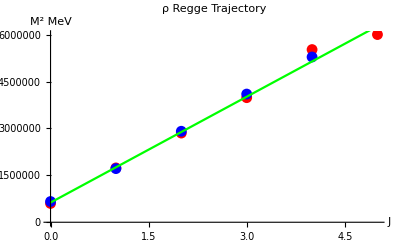

```mathematica
lfit=LinearModelFit[PrepareData[ρ770],J,J];
Show[ListPlot[PrepareData[ρ770],PlotStyle->Red],ListPlot[Table[{J,EJ[J,150,0.86 10^-6,√(1/137),1,0.65,1]^2},{J,0,6}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV},PlotLabel-> "ρ Regge Trajectory"]
```

```mathematica
χ2opta[PrepareData[ρ770],0.86 10^-6,150,√(1/137),1,1]/{χ2l[PrepareData[ρ770]][[1]],1}-{0,1}
```

{1.00862,-0.299673}

```mathematica
χ2opta[PrepareData[ρ770],0.9 10^-6,202,√(1/137),1,1]/{χ2l[PrepareData[ρ770]][[1]],1}-{0,1}
```

{0.798921,-0.188227}

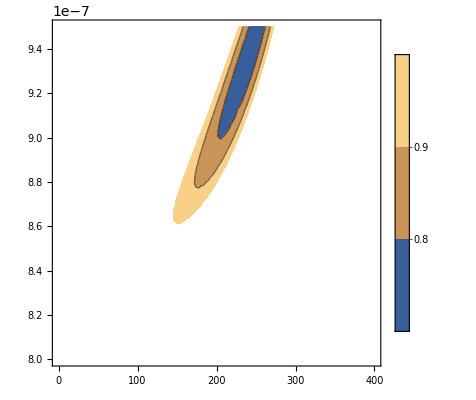

```mathematica
ContourPlot[(χ2opta[PrepareData[ρ770],α,m,√(1/137),1,1][[1]])/(χ2l[PrepareData[ρ770]][[1]]),{m,0,400},{α,0.8 10^-6,0.95 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

```mathematica
ρline={"ρ","0.69-0.89","150-250"};
```

## Fits For ω

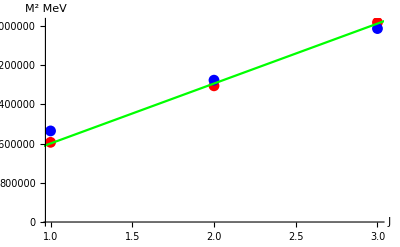

```mathematica
lfit=LinearModelFit[PrepareData[ω],J,J];
Show[ListPlot[PrepareData[ω],PlotStyle->Red],ListPlot[Table[{J,EJ[J,100,0.95 10^-6,0,1,0,1]^2},{J,0,6}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV}]
```

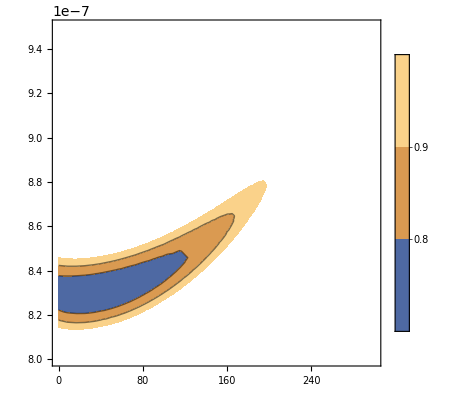

```mathematica
ContourPlot[(χ2opta[PrepareData[ω],α,m,√(1/137),1,1][[1]])/(χ2l[PrepareData[ω]][[1]]),{m,0,300},{α,0.8 10^-6,0.95 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

```mathematica
χ2opta[PrepareData[ω],0.83 10^-6,30,√(1/137),1,1][[2]]
```

0.407044

```mathematica
aω=0.4070440761681316
aωD=π/4(aω-1)-0.479/137+1
```

0.407044

0.530797

```mathematica
χ2opta[PrepareData[ω],0.87 10^-6,170,√(1/137),1,1][[2]]
```

```mathematica
0.8356305959853613//π/4(#-1)-0.479/137+1&
```

0.867408

```mathematica
χ2opta[PrepareData[ω],0.88 10^-6,195,√(5/9)√(1/137),-1,1]
```

{0.000174328,0.907342}

```mathematica
ωline={"ω","0.82-0.867","0-167"};
```

## Fits For η -check

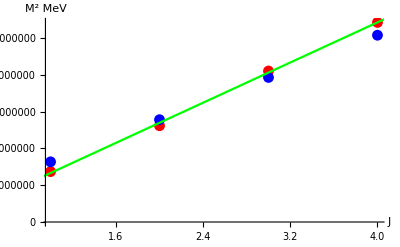

```mathematica
lfit=LinearModelFit[PrepareData[η],J,J];
Show[ListPlot[PrepareData[η],PlotStyle->Red],ListPlot[Table[{J,EJ[J,100,0.88 10^-6,0,1,-0.5,0]^2},{J,0,6}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV}]
```

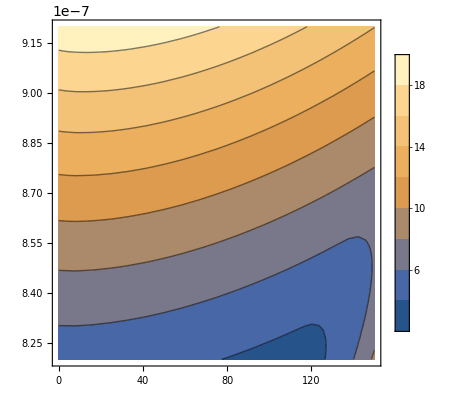

```mathematica
ContourPlot[(χ2opta[PrepareData[η],α,m,√(1/137),1,0][[1]])/(χ2l[PrepareData[η]][[1]]),{m,0,150},{α,0.82 10^-6,0.92 10^-6},PlotLegends->Automatic,PlotPoints->10]
savefile[];
```

```mathematica
χ2opta[PrepareData[η],0.735 10^-6,0,√(1/137),1,0][[2]]
```

-0.000134894

```mathematica
χ2opta[PrepareData[η],0.767 10^-6,56,√(1/137),1,0][[2]]
```

-0.00135886

```mathematica
χ2opta[PrepareData[η],0.75 10^-6,0,√(5/9)√(1/137),-1,0][[1]]
```

0.000348238

```mathematica
(χ2opta[PrepareData[η],0.75 10^-6,0,√(1/137),1,0][[1]])/(χ2l[PrepareData[η]][[1]])
```

0.762345

```mathematica
χ2l[PrepareData[η]][[1]]
```

0.000456833

```mathematica
ηline={"η","0.735-0.765","0-60"};
```

## Fits For a_0 -check

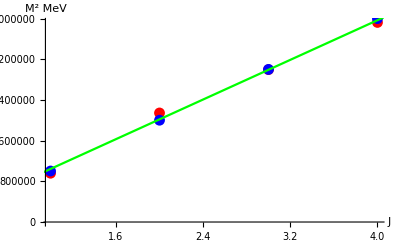

```mathematica
lfit=LinearModelFit[PrepareData[az],J,J];
Show[ListPlot[PrepareData[az],PlotStyle->Red],ListPlot[Table[{J,EJ[J,0,1 10^-6,√(1/137),1,1,1]^2},{J,0,6}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV}]
```

InterpolatingFunction::dmval: Input value {0.978238} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

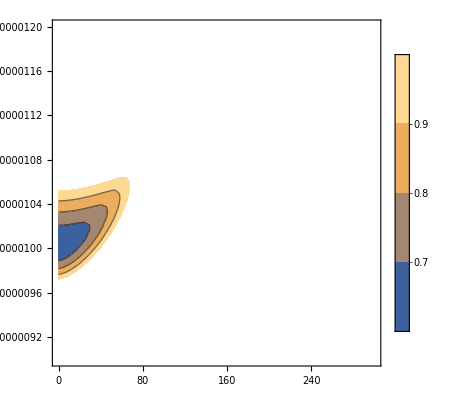

```mathematica
ContourPlot[(χ2opta[PrepareData[az],α,m,√(1/137),1,1][[1]])/(χ2l[PrepareData[az]][[1]]),{m,0,300},{α,0.9 10^-6,1.2 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

```mathematica
aline={"a_0","0.97-1.06","0-67"};
```

## Fits For ϕ -check

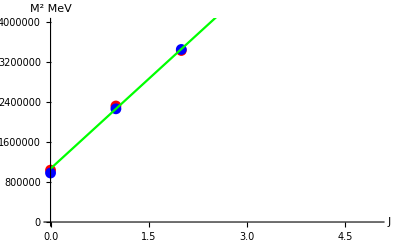

```mathematica
lfit=LinearModelFit[PrepareData[ϕ],J,J];
Show[ListPlot[PrepareData[ϕ],PlotStyle->Red],ListPlot[Table[{J,EJ[J,400,1 10^-6,√(1/137),1,0.95,1]^2},{J,0,2}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV},PlotRange->{Automatic,{-1,4 10^6}}]
```

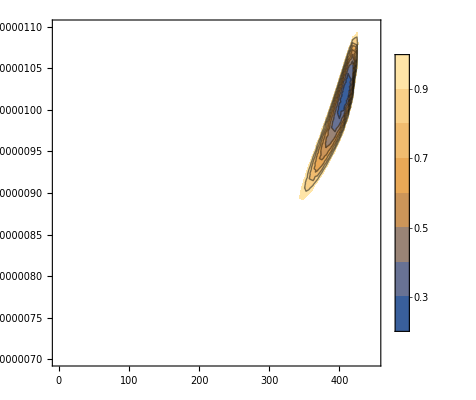

```mathematica
ContourPlot[(χ2opta[PrepareData[ϕ],α,m,√(1/137),1,1][[1]])/(χ2l[PrepareData[ϕ]][[1]]),{m,0,450},{α,0.7 10^-6,1.1 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

```mathematica
χ2opta[PrepareData[ϕ],0.9 10^-6,350,√(1/137),1,1][[2]]
```

0.862669

```mathematica
χ2opta[PrepareData[ϕ],1.09 10^-6,450,√(1/137),1,1][[2]]
```

0.989993

```mathematica
ϕline={"ϕ","0.9-1.09","350-450"};
```

## Fits For κ

```mathematica
(*note that J=5 L=4 data point was excluded. In the PDG it sais it is unconfirmed*)
```

{0.896662,-0.205532}

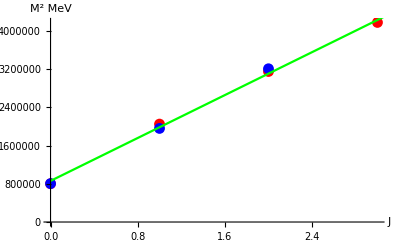

```mathematica
Block[{α=0.86 10^-6,m=250,a,χ},
{χ,a}=χ2opta[PrepareData[κ],α,m,√(1/137),1,1];
lfit=LinearModelFit[PrepareData[κ],J,J];
Print[{χ/(χ2l[PrepareData[κ]][[1]]),a-1}];
Show[ListPlot[PrepareData[κ],PlotStyle->Red],ListPlot[Table[{J,EJ[J,m,α,√(1/137),1,a,1]^2},{J,0,6}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV}]
]
```

```mathematica
ContourPlot[(χ2opta[PrepareData[κ],α,m,√(1/137),1,1][[1]])/(χ2l[PrepareData[κ]][[1]]),{m,150,350},{α,0.8 10^-6,1 10^-6},PlotLegends->Automatic(*,PlotRange->{0,1}*),PlotPoints->10]
savefile[];
```

$Aborted

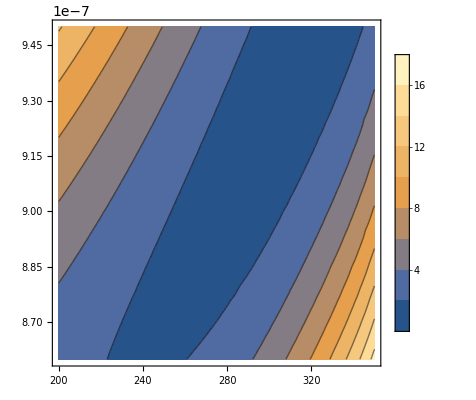

```mathematica
(*19.8.16*)
ContourPlot[(χ2opta[PrepareData[κ],α,m,√(1/137),1,1][[1]])/(χ2l[PrepareData[κ]][[1]]),{m,200,350},{α,0.86 10^-6,0.95 10^-6},PlotLegends->Automatic(*,PlotRange->{0,1}*),PlotPoints->10]
savefile[];
```

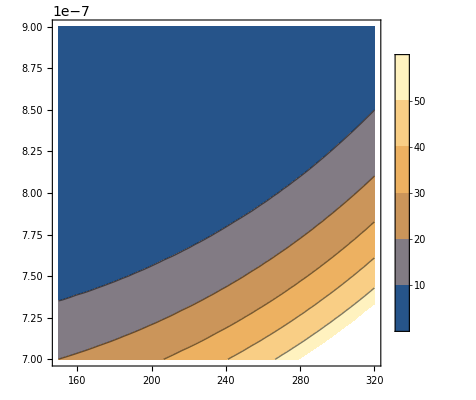

```mathematica
(*19.8.16*)
ContourPlot[(χ2opta[PrepareData[κ],α,m,√(1/137),1,1][[1]])/(χ2l[PrepareData[κ]][[1]]),{m,150,320},{α,0.7 10^-6,0.9 10^-6},PlotLegends->Automatic(*,PlotRange->{0,1}*),PlotPoints->10]
savefile[];
```

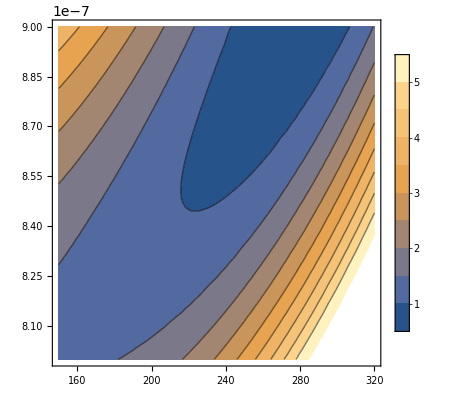

```mathematica
(*22.8.16*)
ContourPlot[(χ2opta[PrepareData[κ],α,m,√(1/137),1,1][[1]])/(χ2l[PrepareData[κ]][[1]]),{m,150,320},{α,0.8 10^-6,0.9 10^-6},PlotLegends->Automatic(*,PlotRange->{0,1}*),PlotPoints->10]
savefile[];
```

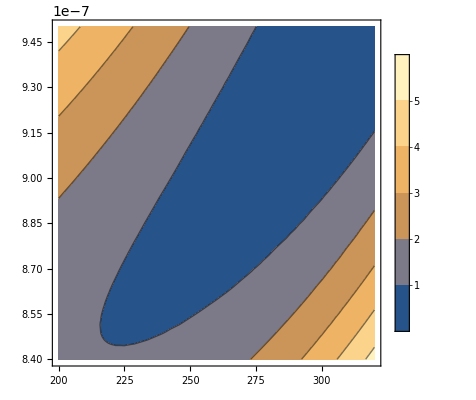

```mathematica
(* Not taking into account the outlying state which is unconfirmed *)
ContourPlot[(χ2opta[PrepareData[κ],α,m,√(1/137),1,1][[1]])/(χ2l[PrepareData[κ]][[1]]),{m,200,320},{α,0.84 10^-6,0.95 10^-6},PlotLegends->Automatic(*,PlotRange->{0,1}*),PlotPoints->10]
savefile[];
```

```mathematica
χ2opta[PrepareData[κ],0.86 10^-6,237,√(1/137),1,1]/{χ2l[PrepareData[κ]][[1]],1}-{0,1}
```

{0.873783,-0.236278}

```mathematica
χ2opta[PrepareData[κ],0.9 10^-6,274,√(1/137),1,1]/{χ2l[PrepareData[κ]][[1]],1}-{0,1}
```

{0.583363,-0.16619}

```mathematica
κline={"κ","0.86-0.95","240-317"};
```

## Fits For K -check

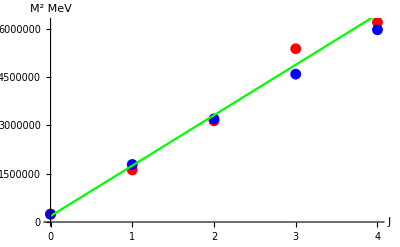

```mathematica
lfit=LinearModelFit[PrepareData[Kzero],J,J];
Show[ListPlot[PrepareData[Kzero],PlotStyle->Red],ListPlot[Table[{J,EJ[J,200,0.75 10^-6,1/3 √(1/137),-1,0.9899999831686782,1]^2},{J,0,6}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV}]
```

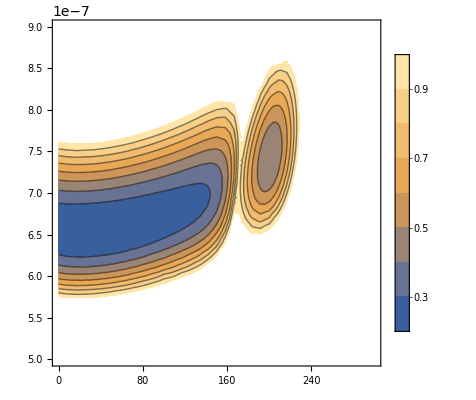

```mathematica
ContourPlot[(χ2opta[PrepareData[Kzero],α,m,1/3 √(1/137),-1,1][[1]])/(χ2l[PrepareData[Kzero]][[1]]),{m,0,300},{α,0.5 10^-6,0.9 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

intercepts for mass differences

```mathematica
χ2opta[PrepareData[Kzero],0.628 10^-6,0,1/3 √(1/137),-1,1]
```

```mathematica
χ2opta[PrepareData[Kzero],0.786 10^-6,206,1/3 √(1/137),-1,1]
```

```mathematica
χ2opta[PrepareData[Kzero],0.7 10^-6,145,1/3 √(1/137),-1,1]
```

```mathematica
Kline={"K","0.824-0.95","0-200"};
```

## symmetric Fits For D spin=0

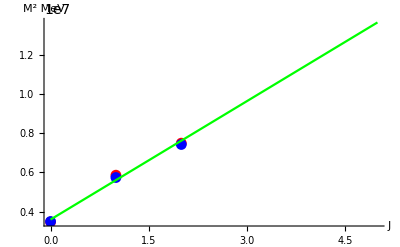

```mathematica
lfit=LinearModelFit[PrepareData[Dz],J,J];
Show[ListPlot[PrepareData[Dz],PlotStyle->Red],ListPlot[Table[{J,EJ[J,900,0.9 10^-6,√(1/137),1,-1.463012977964453*^-7,0]^2},{J,0,2}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV},PlotRange->All]
```

```mathematica
χ2opta[PrepareData[Dz],0.9 10^-6,900,√(1/137),1,0]
```

InterpolatingFunction::dmval: Input value {5.90915×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0000119646} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{0.000180177,-1.46301×10^-7}

#### symmetric fit χ^2 plot

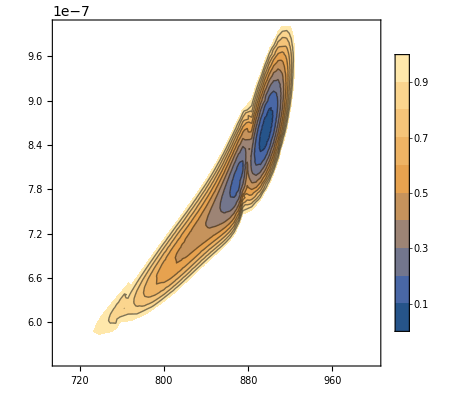

```mathematica
ContourPlot[(χ2opta[PrepareData[Dz],α,m,√(1/137),1,0][[1]])/(χ2l[PrepareData[Dz]][[1]]),{m,700,1000},{α,0.55 10^-6,1 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

```mathematica
χ2opta[PrepareData[Dz],0.8 10^-6,870,√(1/137),1,0]/{χ2l[PrepareData[Dz]][[1]],1}
```

{0.154109,-0.0123359}

```mathematica
χ2opta[PrepareData[Dz],0.86 10^-6,897,√(1/137),1,0]/{χ2l[PrepareData[Dz]][[1]],1}
```

{0.0463984,-9.15325×10^-6}

```mathematica
χ2opta[PrepareData[Dz],0.9 10^-6,904,√(1/137),1,0]/{χ2l[PrepareData[Dz]][[1]],1}
```

InterpolatingFunction::dmval: Input value {9.43248×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.138578,-2.67843×10^-6}

```mathematica
Dline={"D","0.77-0.89","860-900"};
```

## non symmetric Fits For D spin=0 umass=250

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

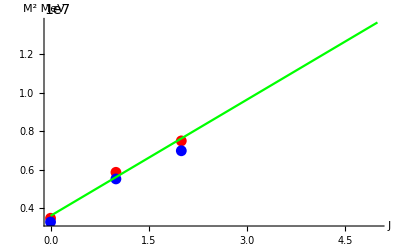

```mathematica
SetUMass[250];
lfit=LinearModelFit[PrepareData[Dz],J,J];
Show[ListPlot[PrepareData[Dz],PlotStyle->Red],ListPlot[Table[{J,EJCharm[J,1490,0.9 10^-6,√(1/137),1,0,0]^2},{J,0,2}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV},PlotRange->All]
```

#### non-symmetric fit χ^2 plot

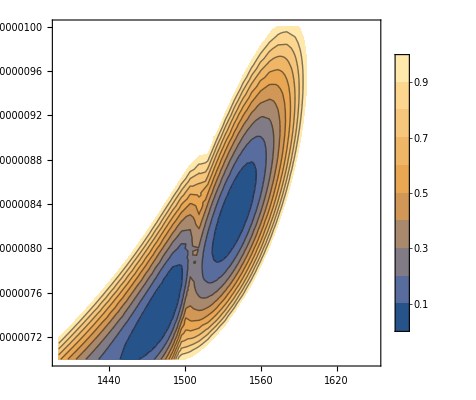

```mathematica
ContourPlot[(χ2optaCharm[PrepareData[Dz],α,m,√(1/137),1,0][[1]])/(χ2l[PrepareData[Dz]][[1]]),{m,1400,1650},{α,0.7 10^-6,1 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

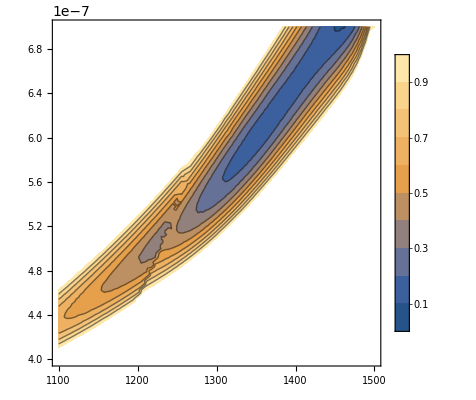

```mathematica
ContourPlot[(χ2optaCharm[PrepareData[Dz],α,m,√(1/137),1,0][[1]])/(χ2l[PrepareData[Dz]][[1]]),{m,1100,1500},{α,0.4 10^-6,0.7 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
```

```mathematica
Dline={"D","0.77-0.89","860-900"};
```

## non symmetric Fits For D spin=0 umass=150

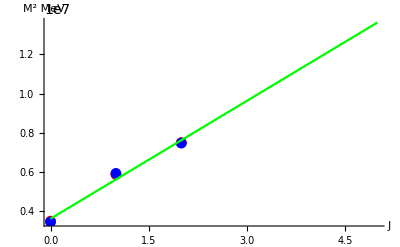

```mathematica
SetUMass[150];
lfit=LinearModelFit[PrepareData[Dz],J,J];
Show[ListPlot[PrepareData[Dz],PlotStyle->Red],ListPlot[Table[{J,EJCharm[J,1631,0.9 10^-6,√(1/137),1,-8.21305901713124*^-6,0]^2},{J,0,2}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV},PlotRange->All]
```

#### non-symmetric fit χ^2 plot

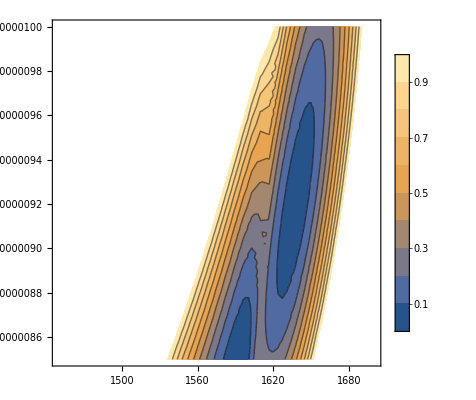

```mathematica
ContourPlot[(χ2optaCharm[PrepareData[Dz],α,m,√(1/137),1,0][[1]])/(χ2l[PrepareData[Dz]][[1]]),{m,1450,1700},{α,0.85 10^-6,1 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

```mathematica
Dline={"D","0.77-0.89","860-900"};
```

## non symmetric Fits For D spin=0 umass=100

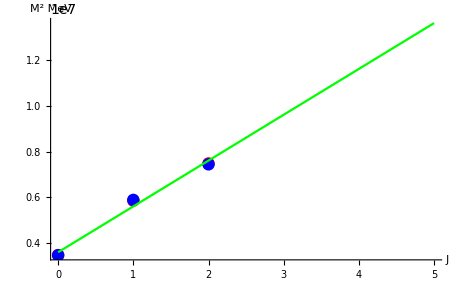

```mathematica
SetUMass[100];
lfit=LinearModelFit[PrepareData[Dz],J,J];
Show[ListPlot[PrepareData[Dz],PlotStyle->Red],ListPlot[Table[{J,EJCharm[J,1645,0.9 10^-6,√(1/137),1,-0.01253713229769228,0]^2},{J,0,2}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV},PlotRange->All]
```

#### non-symmetric fit χ^2 plot umass=100

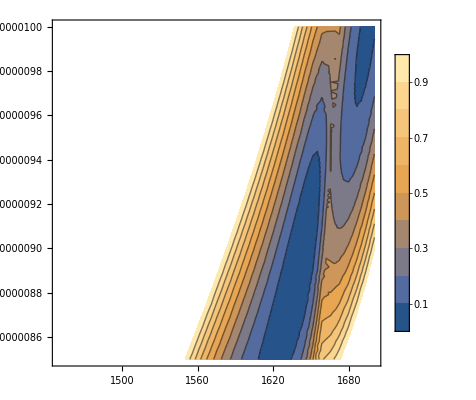

```mathematica
ContourPlot[(χ2optaCharm[PrepareData[Dz],α,m,√(1/137),1,0][[1]])/(χ2l[PrepareData[Dz]][[1]]),{m,1450,1700},{α,0.85 10^-6,1 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

```mathematica
Dline={"D","0.77-0.89","860-900"};
```

## non symmetric Fits For D spin=0 umass=50

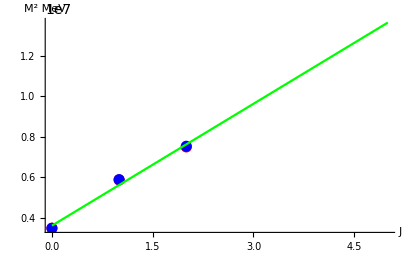

```mathematica
SetUMass[50];
lfit=LinearModelFit[PrepareData[Dz],J,J];
Show[ListPlot[PrepareData[Dz],PlotStyle->Red],ListPlot[Table[{J,EJCharm[J,1600,0.8 10^-6,√(1/137),1,-0.05,0]^2},{J,0,2}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV},PlotRange->All]
```

#### non-symmetric fit χ^2 plot umass=50

```mathematica
ContourPlot[(χ2optaCharm[PrepareData[Dz],α,m,√(1/137),1,0][[1]])/(χ2l[PrepareData[Dz]][[1]]),{m,1450,1700},{α,0.85 10^-6,1 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

-Graphics-

```mathematica
Dline={"D","0.77-0.89","860-900"};
```

## non symmetric Fits For D spin=0 umass=5

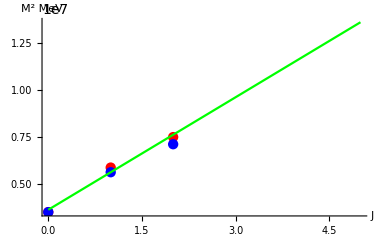

```mathematica
SetUMass[5];
lfit=LinearModelFit[PrepareData[Dz],J,J];
Show[ListPlot[PrepareData[Dz],PlotStyle->Red],ListPlot[Table[{J,EJCharm[J,1584,0.9 10^-6,√(1/137),1,-0.1,0]^2},{J,0,2}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV},PlotRange->All]
```

#### non-symmetric fit χ^2 plot umass=5

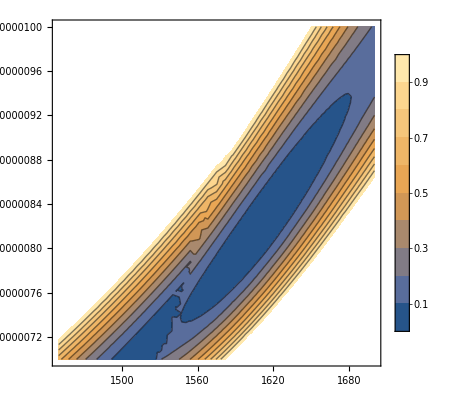

```mathematica
ContourPlot[(χ2optaCharm[PrepareData[Dz],α,m,√(1/137),1,0][[1]])/(χ2l[PrepareData[Dz]][[1]]),{m,1450,1700},{α,0.7 10^-6,1 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

```mathematica
Dline={"D","0.77-0.89","860-900"};
```

## Asymmetric D fits sum up table

```mathematica
Grid[Partition[Flatten[Prepend[Flatten[DTable[{
{250,0.45,1100},{250,0.45,1185},{250,0.86,1499},{250,0.86,1548},{250,0.86,1583}
,{150,0.9,1568},{150,0.9,1633},{150,0.9,1668},{150,0.86,1544},{150,0.86,1594}
,{100,0.86,1560},{100,0.86,1628},{100,0.86,1677},{100,0.9,1585},{100,0.9,1699}
,{50,0.86,1594},{50,0.86,1594},{50,0.9,1594},{50,0.9,1594}
,{5,0.7,1450},{5,0.7,1578},{5,0.86,1569},{5,0.86,1695}}]],{"u Mass[MeV]","α'[GeV^-2]","charm Mass[MeV]","ã","m_d-m_u[MeV]","χ_m/χ_l"}]],6],Frame->All]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {8.0218×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.34596×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7.07615×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

u Mass[MeV] | α'[GeV^-2] | charm Mass[MeV] | ã | m_d-m_u[MeV] | χ_m/χ_l
250 | 0.45 | 1100 | -0.18817 | -1.91596 | 0.729883
250 | 0.45 | 1185 | -0.12005 | -3.6112 | 0.877145
250 | 0.86 | 1499 | -0.0123432 | -14.8343 | 0.875704
250 | 0.86 | 1548 | -4.08911×10^-6 | -29.9253+48.974 ⅈ | 0.045734
250 | 0.86 | 1583 | -2.76495×10^-6 | -29.9112+48.984 ⅈ | 0.943584
150 | 0.9 | 1568 | -0.0332685 | -6.59646 | 0.957694
150 | 0.9 | 1633 | -5.03476×10^-6 | -29.1554+47.8663 ⅈ | 0.0726242
150 | 0.9 | 1668 | -2.21647×10^-7 | -29.1052+47.9019 ⅈ | 0.862301
150 | 0.86 | 1544 | -0.0440218 | -5.30454 | 0.966513
150 | 0.86 | 1594 | -0.0121335 | -15.0193 | 0.0329892
100 | 0.86 | 1560 | -0.0601328 | -3.82673 | 0.915026
100 | 0.86 | 1628 | -0.0210648 | -9.96614 | 0.0435475
100 | 0.86 | 1677 | -1.92362×10^-6 | -29.9022+48.9903 ⅈ | 0.920127
100 | 0.9 | 1585 | -0.0503923 | -4.42282 | 0.941341
100 | 0.9 | 1699 | -2.70436×10^-6 | -29.1311+47.8835 ⅈ | 0.945629
50 | 0.86 | 1594 | -0.0656124 | -3.45495 | 0.366566
50 | 0.86 | 1594 | -0.0656124 | -3.45495 | 0.366566
50 | 0.9 | 1594 | -0.0697484 | -3.02502 | 0.923992
50 | 0.9 | 1594 | -0.0697484 | -3.02502 | 0.923992
5 | 0.7 | 1450 | -0.189254 | -0.575249 | 0.638414
5 | 0.7 | 1578 | -0.0732576 | -3.85187 | 0.889484
5 | 0.86 | 1569 | -0.117835 | -1.34976 | 0.895545
5 | 0.86 | 1695 | -0.0331161 | -6.88527 | 0.935499

```mathematica
Grid[Partition[Flatten[Prepend[Flatten[DTableMod[{
{250,0.45,1100},{250,0.45,1185},{250,0.86,1499},{250,0.86,1548},{250,0.86,1583}
,{150,0.9,1568},{150,0.9,1633},{150,0.9,1668},{150,0.86,1544},{150,0.86,1594}
,{100,0.86,1560},{100,0.86,1628},{100,0.86,1677},{100,0.9,1585},{100,0.9,1699}
,{50,0.86,1594},{50,0.86,1594},{50,0.9,1594},{50,0.9,1594}
,{5,0.7,1450},{5,0.7,1578},{5,0.86,1569},{5,0.86,1695}}]],{"u Mass[MeV]","α'[GeV^-2]","charm Mass[MeV]","ã","m_d-m_u[MeV]","χ_m/χ_l"}]],6],Frame->All]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {8.0218×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.34596×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7.07615×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

u Mass[MeV] | α'[GeV^-2] | charm Mass[MeV] | ã | m_d-m_u[MeV] | χ_m/χ_l
250 | 0.45 | 1100 | -0.18817 | 1.42702 | 0.729883
250 | 0.45 | 1185 | -0.12005 | 0.579401 | 0.877145
250 | 0.86 | 1499 | -0.0123432 | -5.03214 | 0.875704
250 | 0.86 | 1548 | -4.08911×10^-6 | -12.5777+24.487 ⅈ | 0.045734
250 | 0.86 | 1583 | -2.76495×10^-6 | -12.5706+24.492 ⅈ | 0.943584
150 | 0.9 | 1568 | -0.0332685 | -0.913231 | 0.957694
150 | 0.9 | 1633 | -5.03476×10^-6 | -12.1927+23.9332 ⅈ | 0.0726242
150 | 0.9 | 1668 | -2.21647×10^-7 | -12.1676+23.9509 ⅈ | 0.862301
150 | 0.86 | 1544 | -0.0440218 | -0.267272 | 0.966513
150 | 0.86 | 1594 | -0.0121335 | -5.12466 | 0.0329892
100 | 0.86 | 1560 | -0.0601328 | 0.471635 | 0.915026
100 | 0.86 | 1628 | -0.0210648 | -2.59807 | 0.0435475
100 | 0.86 | 1677 | -1.92362×10^-6 | -12.5661+24.4952 ⅈ | 0.920127
100 | 0.9 | 1585 | -0.0503923 | 0.173589 | 0.941341
100 | 0.9 | 1699 | -2.70436×10^-6 | -12.1806+23.9418 ⅈ | 0.945629
50 | 0.86 | 1594 | -0.0656124 | 0.657524 | 0.366566
50 | 0.86 | 1594 | -0.0656124 | 0.657524 | 0.366566
50 | 0.9 | 1594 | -0.0697484 | 0.872489 | 0.923992
50 | 0.9 | 1594 | -0.0697484 | 0.872489 | 0.923992
5 | 0.7 | 1450 | -0.189254 | 2.09738 | 0.638414
5 | 0.7 | 1578 | -0.0732576 | 0.459065 | 0.889484
5 | 0.86 | 1569 | -0.117835 | 1.71012 | 0.895545
5 | 0.86 | 1695 | -0.0331161 | -1.05764 | 0.935499

## Fits For (D^*)_s -check

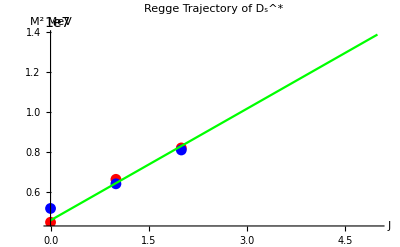

```mathematica
lfit=LinearModelFit[PrepareData[Dss],J,J];
Show[ListPlot[PrepareData[Dss],PlotStyle->Red],ListPlot[Table[{J,EJ[J,800,0.7195 10^-6,√(1/137),1,0.5,1]^2},{J,0,2}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV},PlotRange->All,PlotLabel-> "Regge Trajectory of D_s^*"]
```

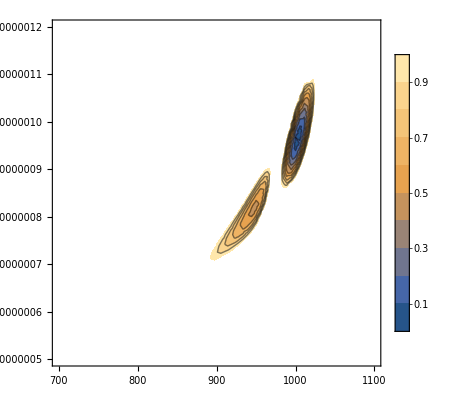

```mathematica
ContourPlot[(χ2opta[PrepareData[Dss],α,m,√(1/137),1,1][[1]])/(χ2l[PrepareData[Dss]][[1]]),{m,700,1100},{α,0.5 10^-6,1.2 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

```mathematica
χ2opta[PrepareData[Dss],0.7195 10^-6,895,√(1/137),1,1][[2]]
```

0.885597

```mathematica
χ2opta[PrepareData[Dss],1.081 10^-6,1015,√(1/137),1,1][[2]]
```

0.989981

```mathematica
χ2opta[PrepareData[Dss],0.7195 10^-6,895,√(1/137),1,1][[1]]
```

0.000448887

```mathematica
χ2opta[PrepareData[Dss],1.081 10^-6,1015,√(1/137),1,1][[1]]
```

0.000408413

```mathematica
χ2opta[PrepareData[Dss],0.95 10^-6,1000,√(1/137),1,1][[1]]
```

0.0000349889

## Fits For B -check

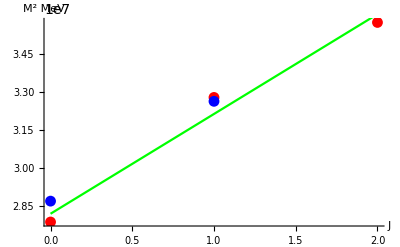

```mathematica
lfit=LinearModelFit[PrepareData[B],J,J];
Show[ListPlot[PrepareData[B],PlotStyle->Red],ListPlot[Table[{J,EJ[J,2500,0.5 10^-6,0,-1,-0.1,0]^2},{J,0,3}],PlotStyle->Blue],Plot[lfit[J],{J,0,3},PlotStyle->Green],AxesLabel-> {J,M^2 MeV}]
```

```mathematica
ContourPlot[(χ2opta[PrepareData[B],α,m,1/3 √(1/137),-1,0][[1]])/(χ2l[PrepareData[B]][[1]]),{m,2450,2700},{α,0.45 10^-6,0.95 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

FindMinimum::nrnum: The function value 0.000261923  + 5.46756×10^-11\ ⅈ is not a real number at {a$14607349} = {-0.1}.

ReplaceAll::reps: {a$14607349} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

FindMinimum::nrnum: The function value 0.000607729  + 4.74618×10^-11\ ⅈ is not a real number at {a$14619386} = {-0.1}.

ReplaceAll::reps: {a$14619386} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

intercepts for mass differences

```mathematica
χ2opta[PrepareData[B],0.85 10^-6,2635,1/3 √(1/137),-1,0][[2]]
```

```mathematica
χ2opta[PrepareData[B],0.85 10^-6,2650,1/3 √(1/137),-1,0][[2]]
```

```mathematica
Bline={"B","0.8-0.9","2630-2650"};
```

## Fits For Υ

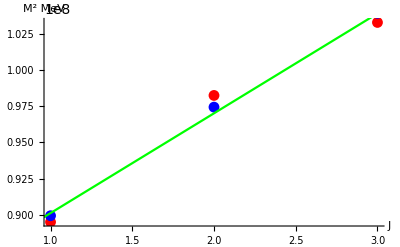

```mathematica
lfit=LinearModelFit[PrepareData[Υ],J,J];
Show[ListPlot[PrepareData[Υ],PlotStyle->Red],ListPlot[Table[{J,EJ[J,4400,0.35 10^-6,√(1/137),1,0.5,1/2]^2},{J,0,5}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV}]
```

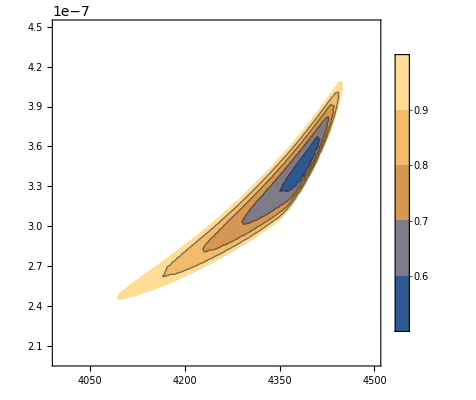

```mathematica
ContourPlot[(χ2opta[PrepareData[Υ],α,m,√(1/137),1,1/2][[1]])/(χ2l[PrepareData[Υ]][[1]]),{m,4000,4500},{α,0.2 10^-6,0.45 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

```mathematica
χ2opta[PrepareData[Υ],0.25 10^-6,4100,√(1/137),1,1/2][[2]]
```

```mathematica
χ2opta[PrepareData[Υ],4 10^-6,4450,√(1/137),1,1/2][[2]]
```

```mathematica
ϒline={"ϒ","0.32-0.36","4350-4410"};
```

## Fits For p/n

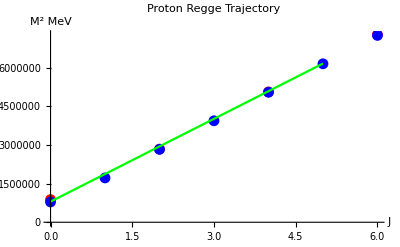

```mathematica
lfit=LinearModelFit[PrepareData[p],J,J];
Show[ListPlot[PrepareData[p],PlotStyle->Red],ListPlot[Table[{J,EJ[J,150,0.92 10^-6,0,1,0,1/2]^2},{J,0,6}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV},PlotLabel-> "Proton Regge Trajectory"]
```

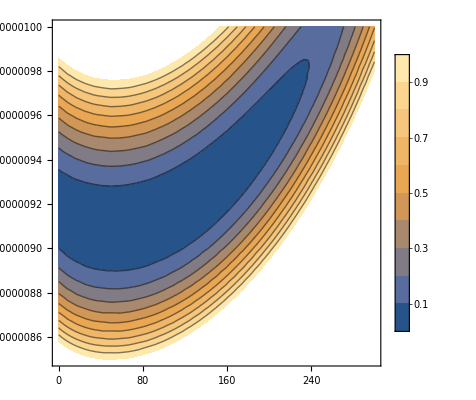

```mathematica
ContourPlot[(χ2opta[PrepareData[p],α,m,√(1/137),1,1/2][[1]])/(χ2l[PrepareData[p]][[1]]),{m,0,300},{α,0.85 10^-6,1 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
```

```mathematica
χ2opta[PrepareData[p],0.85 10^-6,50,√(1/137),1,1/2][[2]]
```

```mathematica
-0.4050295121674653-0.5
```

-0.90503

```mathematica
χ2opta[PrepareData[p],0.985 10^-6,240,√(1/137),1,1/2][[2]]
```

```mathematica
0.18399540189527042-0.5
```

-0.316005

```mathematica
0.1854672868068975-0.5
```

-0.314533

```mathematica
protonline={"Proton","0.893-0.985","0-240.5"};
```

## Fits For Λ -check

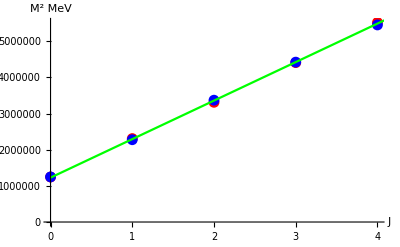

```mathematica
lfit=LinearModelFit[PrepareData[Λ],J,J];
Show[ListPlot[PrepareData[Λ],PlotStyle->Red],ListPlot[Table[{J,EJ[J,400,1.078 10^-6,1/3 √(1/137),-1,χ2opta[PrepareData[Λ],1.078 10^-6,400,1/3 √(1/137),-1,1/2][[2]],1/2]^2},{J,0,6}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV}]
```

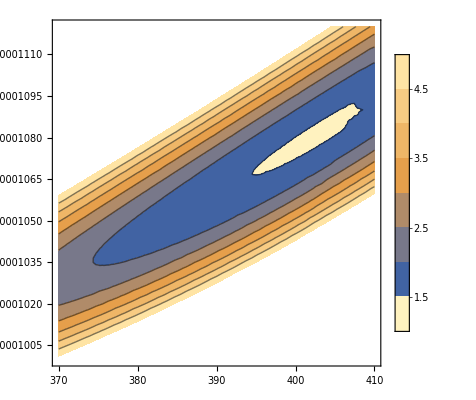

```mathematica
ContourPlot[(χ2opta[PrepareData[Λ],α,m,1/3 √(1/137),-1,1/2][[1]])/(χ2l[PrepareData[Λ]][[1]]),{m,370,410},{α,1 10^-6,1.12 10^-6},PlotLegends->Automatic,PlotRange->{0,5},PlotPoints->10]
savefile[];
```

```mathematica
χ2opta[PrepareData[Λ],1.067 10^-6,395,1/3 √(1/137),-1,1/2][[2]]
```

0.329308

```mathematica
χ2opta[PrepareData[Λ],1.09 10^-6,408,1/3 √(1/137),-1,1/2][[2]]
```

0.355001

```mathematica
Λline={"Λ","1.067-1.09","395-408"};
```

## Fits For Σ

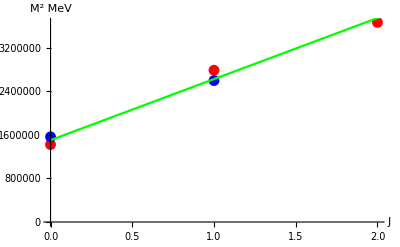

```mathematica
lfit=LinearModelFit[PrepareData[Σ0],J,J];
Show[ListPlot[PrepareData[Σ0],PlotStyle->Red],ListPlot[Table[{J,EJ[J,300,0.8 10^-6,√(1/137),1,0,1/2]^2},{J,0,2}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV}]
```

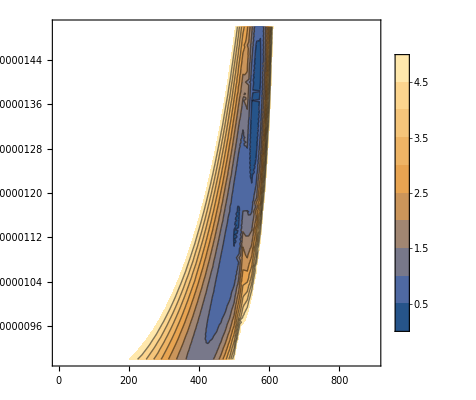

```mathematica
ContourPlot[(χ2opta[PrepareData[Σ0],α,m,√(1/137),1,1/2][[1]])/(χ2l[PrepareData[Σ0]][[1]]),{m,0,900},{α,0.9 10^-6,1.5 10^-6},PlotLegends->Automatic,PlotRange->{0,5},PlotPoints->10]
savefile[];
```

```mathematica
χ2opta[PrepareData[Σ0],0.9 10^-6,405,1/3 √(1/137),-1,1/2]-{0,1/2}
```

{0.00264193,-0.212864}

```mathematica
χ2opta[PrepareData[Σ0],0.95 10^-6,420,1/3 √(1/137),-1,1/2]-{0,1/2}
```

{0.00238027,-0.193514}

```mathematica
χ2opta[PrepareData[Σ0],1 10^-6,454,1/3 √(1/137),-1,1/2]-{0,1/2}
```

{0.0018624,-0.131228}

```mathematica
χ2l[PrepareData[Σ0]][[1]]
```

```mathematica
Σline={"Σ","0.95-1.45","400-580"};
```

## Fits For Ξ

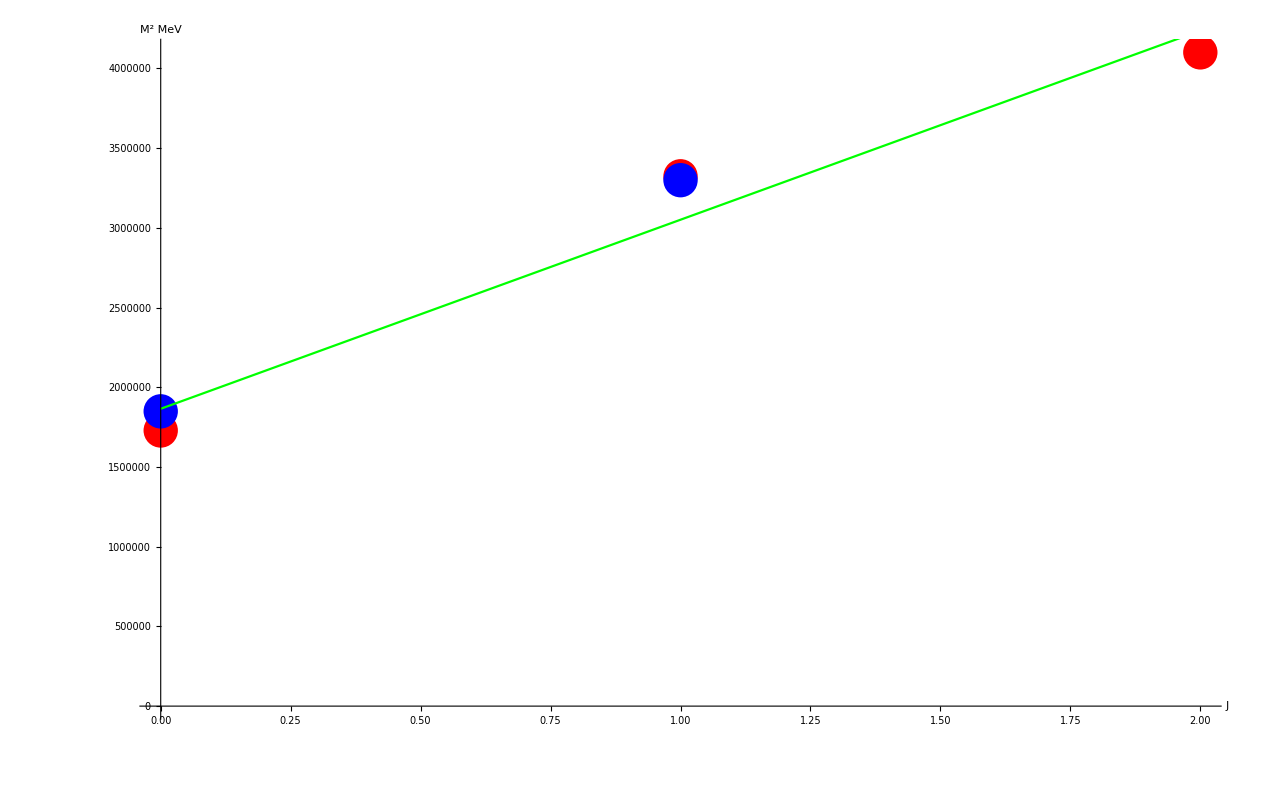

```mathematica
lfit=LinearModelFit[PrepareData[Ξ],J,J];
Show[ListPlot[PrepareData[Ξ],PlotStyle->Red],ListPlot[Table[{J,EJ[J,650,1.3 10^-6,√(1/137),1,0.5,1/2]^2},{J,0,2}],PlotStyle->Blue],Plot[lfit[J],{J,0,5},PlotStyle->Green],AxesLabel-> {J,M^2 MeV}]
```

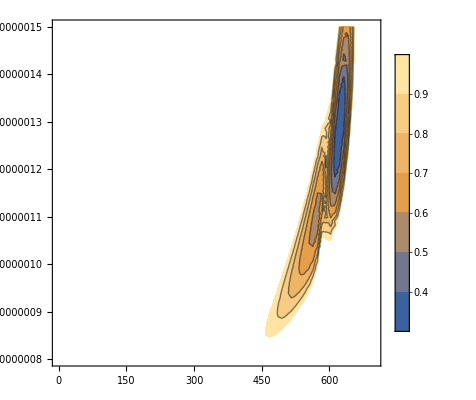

```mathematica
ContourPlot[(χ2opta[PrepareData[Ξ],α,m,√(1/137),1,1/2][[1]])/(χ2l[PrepareData[Ξ]][[1]]),{m,0,700},{α,0.8 10^-6,1.5 10^-6},PlotLegends->Automatic,PlotRange->{0,1},PlotPoints->10]
savefile[];
```

```mathematica
χ2opta[PrepareData[Ξ],0.9 10^-6,497,√(1/137),1,1/2]-{0,1/2}
```

{0.00405914,-0.141608}

```mathematica
χ2opta[PrepareData[Ξ],0.95 10^-6,525,√(1/137),1,1/2]-{0,1/2}
```

{0.00353453,-0.102099}

```mathematica
χ2opta[PrepareData[Ξ],1 10^-6,547,√(1/137),1,1/2]-{0,1/2}
```

{0.00306888,-0.0722259}

```mathematica
Ξline={"Ξ","0.84-1.5","460-660"};
```

## Summary Tables

## Mesons

```mathematica
Grid[{{"Hadron","α'[Gev^-2]","Endpoint Masses[MeV]"},πline,ρline,ωline,ηline,aline,ϕline,κline,Kline,Dline,Bline,ϒline},Frame->All]
```

Hadron | α'[Gev^-2] | Endpoint Masses[MeV]
π | 0.82-0.86 | 100-170
ρ | 0.86-1 | 150-300
ω | 0.82-0.867 | 0-167
η | 0.735-0.765 | 0-60
a_0 | 0.97-1.06 | 0-67
ϕ | 1.42-1.6 | 450-500
κ | 0.95-0.99 | 320-340
K | 0.824-0.95 | 0-200
D | 0.77-0.89 | 860-900
B | 0.8-0.9 | 2630-2650
ϒ | 0.32-0.36 | 4350-4410

## Baryons

```mathematica
Grid[{{"Hadron","α'[Gev^-2]","Endpoint Masses[MeV]"},protonline,Λline,Σline,Ξline},Frame->All]
```

Hadron | α'[Gev^-2] | Endpoint Masses[MeV]
Proton | 0.893-0.985 | 0-240.5
Λ | 1.067-1.09 | 395-408
Σ | 0.95-1.45 | 400-580
Ξ | 0.84-1.5 | 460-660

### All Hadrons

```mathematica
Grid[{{"Hadron","α'[Gev^-2]","Endpoint Masses[MeV]"},πline,ρline,ωline,ηline,aline,ϕline,κline,Kline,Dline,Bline,ϒline,protonline,Λline,Σline,Ξline},Frame->All]
```

Hadron | α'[Gev^-2] | Endpoint Masses[MeV]
π | 0.82-0.86 | 100-170
ρ | 0.86-1 | 150-300
ω | 0.82-0.867 | 0-167
η | 0.735-0.765 | 0-60
a_0 | 0.97-1.06 | 0-67
ϕ | 1.42-1.6 | 450-500
κ | 0.95-0.99 | 320-340
K | 0.824-0.95 | 0-200
D | 0.77-0.89 | 860-900
B | 0.8-0.9 | 2630-2650
ϒ | 0.32-0.36 | 4350-4410
Proton | 0.893-0.985 | 0-240.5
Λ | 1.067-1.09 | 395-408
Σ | 0.95-1.45 | 400-580
Ξ | 0.84-1.5 | 460-660